## Problems: Torque Control With a Swarm of Normally distributed Particles Under Global Control Given a swarm of particles, whose positions are normally distributed, and a pivoted object, where should the swarm hit to generate the maximum torque? related problem: shooting a railroad track switch with a shotgun. F = force provided by entire swarm N = number of particles F/N = force per particle ⅇ^(-(x-μ)^2/(2 σ^2))

### Problem 1: marginalizing to 1 dimension, not thinking about distributed time of impact this is only a one-pass of the swarm at the object. The kilobots are pushing continuously. (math is for one step, real world is an iterative process)

```mathematica
pdfNormal[x_,μ_,σ_]:=1/(√(2 π) σ) ⅇ^(-(x-μ)^2/(2 σ^2))
```

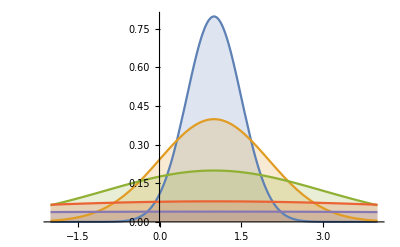

```mathematica
Plot[Evaluate[pdfNormal[x,1,σ]/.σ->{1/2,1,2,5,10}],{x,-2,4},Filling->Axis,PlotRange->All]
```

```mathematica
(*FullSimplify[∫_0^1 x TriangularDistribution[{0,1},1/2]ⅆx]*)
```

1/2 TriangularDistribution[{0,1},1/2]

```mathematica
FullSimplify[∫_0^1 x pdfNormal[x,μ,σ]ⅆx] (*x is the moment arm, we integrate over the length of the object*)
```

((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])

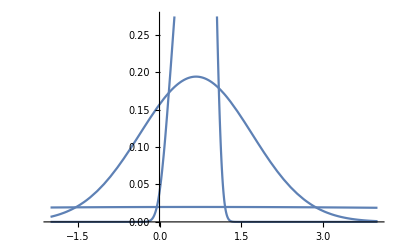
{0.21216,-Graphics-}

```mathematica
Timing[Plot[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])/.σ->{1/10,1,10},{μ,-2,4}]]
```

```mathematica
Timing[Plot[∫_0^1 pdfNormal[x,μ,1]ⅆx,{μ,-2,4}]]
```

$Aborted

```mathematica
Plot[Evaluate[pdf[TriangularDistribution[x,1,σ]/.σ->{1/2,1,2,5,10}],{x,-2,4},Filling->Axis,PlotRange->All]
```

```mathematica
Torque[μ_,σ_]:=((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])
```

```mathematica
(*TorqueTri[μ_] := PDF[TriangularDistribution[{μ-σ√6,μ+σ√6},1/2]];*)
(*FullSimplify[D[TorqueTri[μ],μ]]*)
(*SolveAlways[D[TorqueTri[μ],μ]==0,{μ}];*)
```

```mathematica
FullSimplify[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])]
```

((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])

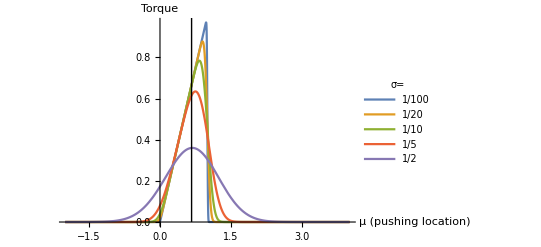

```mathematica
sigs = {1/10,1/2,1,2,5}/10;
(*TODO: place legend inside the plot*)

Plot[Evaluate[Torque[μ,σ]/.{σ->sigs}],{μ,-2,4},PlotRange->All,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.75,0.55}],AxesLabel->{"μ (pushing location)","Torque"},Epilog->{Line[{{2/3,0},{2/3,1}}]}]
```

```mathematica
FullSimplify[D[Torque[μ,σ],μ]]
```

-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])

```mathematica
Minimize[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),μ] (*TODO: check how this function works*)
```

Minimize[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),μ]

```mathematica
DTorque1[μ_,σ_] = (ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)
DTorque2[μ_,σ_] = 1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])
```

0.797885 ⅇ^(-2. (-1+μ)^2)

1/2 (Erf[1.41421 (1-μ)]+Erf[1.41421 μ])

Solve[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])==0,{μ}]

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])==0,{μ}]

```mathematica
(*t = (1/(1+0.47047μ))*)
(*erff[x_] = 1-( 0.278393(1/(1+0.47047x)) -0.0959 (1/(1+0.47047x))^2 + 0.7479 (1/(1+0.47047x))^3) ⅇ^(-x^2)
σ = 0.5;*)
Solve[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (erff[(1-μ)/(√2 σ)]+erff[μ/(√2 σ)])==0,{μ}]
```

```mathematica
a = (8(π -3))/(3π(4-π));
erfff[x_] = Sign[x] √(1-ⅇ^(-x^2(4/π+a x^2)/(1+ a x^2)));
InverseFunction[erfff[x]] =Sign[x]  √(√((2/(πa)+ln(1-x^2)/2)^2- ln(1-x^2)/a)-(2/(πa)+ln(1-x^2)/2))
(*erfff[x_] =*)
SolveAlways[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (erfff[(1-μ)/(√2 σ)]+erfff[μ/(√2 σ)])==0(*&& 0<μ≤1*),{μ}]
```

Set::write: Tag InverseFunction in InverseFunction[√1 - ⅇ^-Power[« 2 »]\ Power[« 2 »]\ Plus[« 2 »]\ Sign[x]] is Protected.

√(-1/2 ln (1-x^2)+√(-(3 ln (4-π) π (1-x^2))/(8 (-3+π))+(1/2 ln (1-x^2)+2/πa)^2)-2/πa) Sign[x]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction :: ifun will be suppressed during this calculation.

$Aborted

```mathematica
a1 = 278/1000;
a2 = 23/100;
a3 = 1/1000;
a4 = 78/1000;
erff[x_] = 1-1/((1+a1 x+ a2 x^2+ a3 x^3+ a4 x^4)^4);
SolveAlways[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (erff[(1-μ)/(√2 σ)]+erff[μ/(√2 σ)])==0,{μ}]
```

$Aborted

```mathematica
FullSimplify[-(ⅇ^(-(-1+μ)^2/(2 σ^2)))/(√(2 π) σ)+1/2 (erfff[(1-μ)/(√2 σ)]+erfff[μ/(√2 σ)])]
```

$Aborted

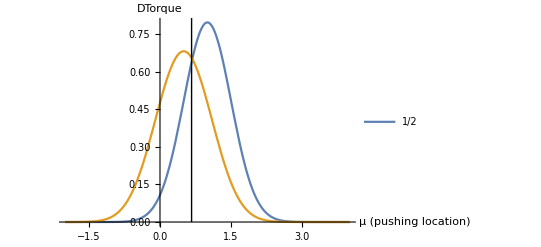

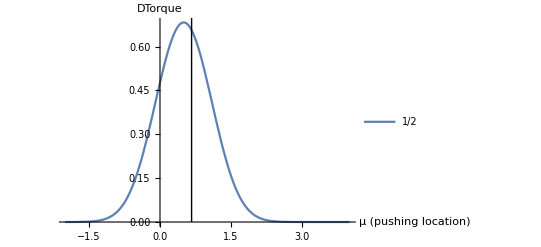

```mathematica
sigs = {5}/10;
(*TODO: place legend inside the plot*)
Plot[{Evaluate[DTorque1[μ,σ]/.{σ->sigs}],Evaluate[DTorque2[μ,σ]/.{σ->sigs}]},{μ,-2,4},PlotRange->All,PlotLegends->sigs,AxesLabel->{"μ (pushing location)","DTorque"},Epilog->{Line[{{2/3,0},{2/3,1}}]}]
Plot[Evaluate[DTorque2[μ,σ]/.{σ->sigs}],{μ,-2,4},PlotRange->All,PlotLegends->sigs,AxesLabel->{"μ (pushing location)","DTorque"},Epilog->{Line[{{2/3,0},{2/3,1}}]}]
```

```mathematica
FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)])/.σ->100,{μ,1}]
```

{0.00199471,{μ→0.666667}}

## TODO : shiva, solve this limit analytically:

### Problem 1: (Normal dist) a pivot point. Where should swarm fit to generate the most torque?

```mathematica
bestPush=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-μ^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[μ/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];
(*FindMaximum[PDF[TorqueTri],{μ,1}];*)
(*FindMaximum[PDF[TriangularDistribution[{0,4},c],x],{c,{1/2,2,3}}]//Evaluate,{x,0,4},Filling->Axis,Exclusions->None*)
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

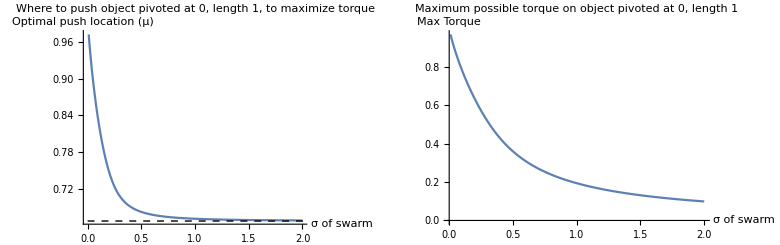

```mathematica
plotBestLocationPivotObject =ListPlot[{Transpose[{bestPush⟦;;,1⟧,bestPush⟦;;,3⟧}](*,
Transpose[{bestPush⟦;;,1⟧,2/3+1/3 ⅇ^(-6.5bestPush⟦;;,1⟧)}]*)},AxesLabel->{"σ of swarm","Optimal push location (μ)"},PlotRange->All,Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}]},

Prolog-> Inset[pivotDrawing[1/10]],
PlotLabel->"Where to push object pivoted at 0, length 1, to maximize torque"];
plotMaxTorquePivotObject=ListPlot[Transpose[{bestPush⟦;;,1⟧,bestPush⟦;;,2⟧}],AxesLabel->{"σ of swarm","Max Torque"},Joined->True,PlotLabel->"Maximum possible torque on object pivoted at 0, length 1",ImageSize->Medium];
GraphicsRow[{plotBestLocationPivotObject,plotMaxTorquePivotObject}]
```

```mathematica
pivotDrawing[σ_]:=Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}]
```

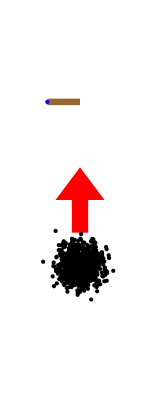
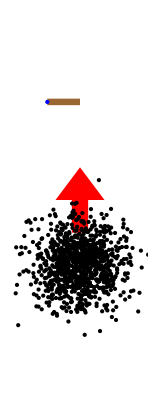
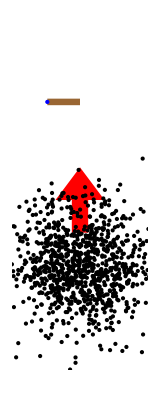
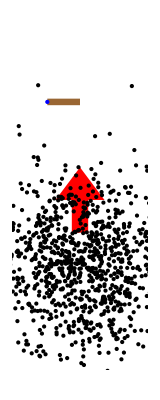

```mathematica
Table[Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/10,1/2,1,2}}]
```

#### Trying to solve analytically is hard for me. Perhaps we can do this, but I’m not sure how so these used a numeric solution.

```mathematica
Maximize[(-ⅇ^(-1/2 (-1+μ)^2)+ⅇ^(-μ^2/2))/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2)]+Erf[μ/(√2)])/.σ-> 1,μ]
```

Maximize[(-ⅇ^(-1/2 (-1+μ)^2)+ⅇ^(-μ^2/2))/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2)]+Erf[μ/(√2)]),μ]

### Problem 1: (Triangle dist) a pivot point. Where should swarm fit to generate the most torque?

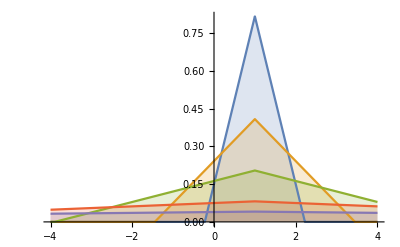

```mathematica
μ=1;
Plot[Table[PDF[TriangularDistribution[{μ-σ√6,μ+σ√6}],x],{σ,{1/2,1,2,5,10}}]//Evaluate,{x,-4,4},Filling->Axis,Exclusions->None,PlotRange->All]
```

```mathematica
x PDF[TriangularDistribution[{μ-σ√6,μ+σ√6}],x]
```

x (Piecewise[{{(x-μ+√6 σ)/(6 σ^2), μ-√6 σ≤x≤μ}, {(-x+μ+√6 σ)/(6 σ^2), μ<x≤μ+√6 σ}, {0, True}}])

```mathematica
∫_0^1 (x (Piecewise[{{(x-μ+√6 σ)/(6 σ^2), μ-√6 σ≤x≤μ}, {(-x+μ+√6 σ)/(6 σ^2), μ<x≤μ+√6 σ}, {0, True}}]))ⅆx
```

Piecewise[{{μ, 0<μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ>0&&σ>0}, {1/6 (3 μ+√6 σ), μ==0&&√6 μ+6 σ<√6&&σ>0}, {(2-3 μ+3 √6 σ)/(36 σ^2), (μ>1&&√6 μ-6 σ≤0)||(μ==1&&σ≥1/(√6))}, {(-2+3 μ+3 √6 σ)/(36 σ^2), μ<0&&√6 μ+6 σ>√6}, {(-2+3 μ-2 μ^3+3 √6 σ)/(36 σ^2), 0<μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ≤0}, {(-2+3 μ-μ^3+3 √6 σ-3 √6 μ^2 σ)/(36 σ^2), (μ==0&&√6 μ+6 σ≥√6)||(0≤μ<1&&√6 μ+6 σ≥√6&&σ≤0&&√6 μ-6 σ>0)}, {(-μ^3+3 √6 μ^2 σ)/(36 σ^2), 0<μ<1&&√6 μ-6 σ≤0&&√6 μ+6 σ<√6&&σ≤0}, {(√6-√6 μ+3 μ σ-√6 σ^2)/(6 σ), μ==1&&0<σ<1/(√6)}, {(-2+3 μ-μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), 0<μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ>0&&σ>0}, {(2-3 μ+μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), μ>1&&0<√6 μ-6 σ<√6}, {(-μ^3+3 √6 μ^2 σ+18 μ σ^2+6 √6 σ^3)/(36 σ^2), 0<μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ≤0&&σ>0}, {(μ^3+3 √6 μ^2 σ+18 μ σ^2+6 √6 σ^3)/(36 σ^2), μ<0&&0<√6 μ+6 σ≤√6}, {0, True}}]

```mathematica
Assuming[σ>0&&μ>0,Refine[Piecewise[{{μ, 0<μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ>0&&σ>0}, {1/6 (3 μ+√6 σ), μ==0&&√6 μ+6 σ<√6&&σ>0}, {(2-3 μ+3 √6 σ)/(36 σ^2), (μ>1&&√6 μ-6 σ≤0)||(μ==1&&σ≥1/(√6))}, {(-2+3 μ+3 √6 σ)/(36 σ^2), μ<0&&√6 μ+6 σ>√6}, {(-2+3 μ-2 μ^3+3 √6 σ)/(36 σ^2), 0<μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ≤0}, {(-2+3 μ-μ^3+3 √6 σ-3 √6 μ^2 σ)/(36 σ^2), (μ==0&&√6 μ+6 σ≥√6)||(0≤μ<1&&√6 μ+6 σ≥√6&&σ≤0&&√6 μ-6 σ>0)}, {(-μ^3+3 √6 μ^2 σ)/(36 σ^2), 0<μ<1&&√6 μ-6 σ≤0&&√6 μ+6 σ<√6&&σ≤0}, {(√6-√6 μ+3 μ σ-√6 σ^2)/(6 σ), μ==1&&0<σ<1/(√6)}, {(-2+3 μ-μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), 0<μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ>0&&σ>0}, {(2-3 μ+μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), μ>1&&0<√6 μ-6 σ<√6}, {(-μ^3+3 √6 μ^2 σ+18 μ σ^2+6 √6 σ^3)/(36 σ^2), 0<μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ≤0&&σ>0}, {(μ^3+3 √6 μ^2 σ+18 μ σ^2+6 √6 σ^3)/(36 σ^2), μ<0&&0<√6 μ+6 σ≤√6}, {0, True}}]]]
```

Piecewise[{{μ, μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ>0}, {(2-3 μ+3 √6 σ)/(36 σ^2), (μ>1&&√6 μ-6 σ≤0)||(μ==1&&σ≥1/(√6))}, {(-2+3 μ-2 μ^3+3 √6 σ)/(36 σ^2), μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ≤0}, {(√6-√6 μ+3 μ σ-√6 σ^2)/(6 σ), μ==1&&σ<1/(√6)}, {(-2+3 μ-μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ>0}, {(2-3 μ+μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), μ>1&&0<√6 μ-6 σ<√6}, {(-μ^3+3 √6 μ^2 σ+18 μ σ^2+6 √6 σ^3)/(36 σ^2), μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ≤0}, {0, True}}]

```mathematica
TorqueTriV2[μ_,σ_]:= Piecewise[{{μ, μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ>0}, {(2-3 μ+3 √6 σ)/(36 σ^2), (μ>1&&√6 μ-6 σ≤0)||(μ==1&&σ≥1/(√6))}, {(-2+3 μ-2 μ^3+3 √6 σ)/(36 σ^2), μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ≤0}, {(√6-√6 μ+3 μ σ-√6 σ^2)/(6 σ), μ==1&&σ<1/(√6)}, {(-2+3 μ-μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), μ<1&&√6 μ+6 σ≥√6&&√6 μ-6 σ>0}, {(2-3 μ+μ^3+3 √6 σ-3 √6 μ^2 σ+18 μ σ^2-6 √6 σ^3)/(36 σ^2), μ>1&&0<√6 μ-6 σ<√6}, {(-μ^3+3 √6 μ^2 σ+18 μ σ^2+6 √6 σ^3)/(36 σ^2), μ<1&&√6 μ+6 σ<√6&&√6 μ-6 σ≤0}, {0, True}}]
```

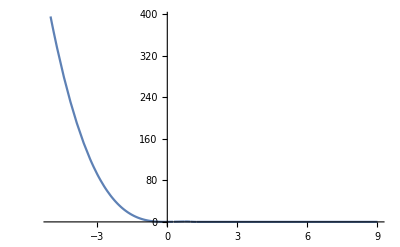

```mathematica
sigs = {1/10,1/2,1,2,5};
(*TODO: place legend inside the plot*)

Plot[Evaluate[TorqueTriV2[μ,1/10]],{μ,-5,9},PlotRange->All(*,PlotLegends->Placed[LineLegend[sigs,LabelStyle->{Black,Bold,8},LegendLabel->"σ="],{0.75,0.85}],AxesLabel->{"μ (pushing location)","Torque"}*)(*,Epilog->{Line[{{2/3,0},{2/3,1}}]}*)]
```

```mathematica
bestPush=Table[ans=FindMaximum[TorqueTriV2[μ,σ],{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];
(*FindMaximum[PDF[TorqueTri],{μ,1}];*)
(*FindMaximum[PDF[TriangularDistribution[{0,4},c],x],{c,{1/2,2,3}}]//Evaluate,{x,0,4},Filling->Axis,Exclusions->None*)
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMaximum :: cvmit will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

$Aborted

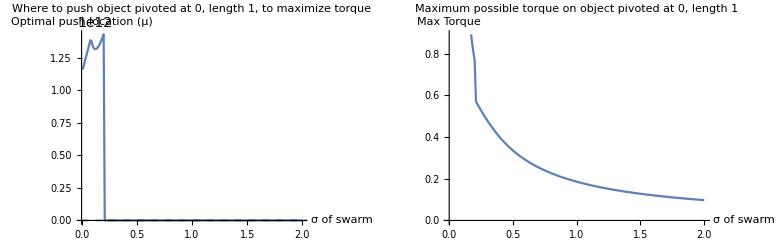

```mathematica
plotBestLocationPivotObject =ListPlot[{Transpose[{bestPush⟦;;,1⟧,bestPush⟦;;,3⟧}](*,
Transpose[{bestPush⟦;;,1⟧,2/3+1/3 ⅇ^(-6.5bestPush⟦;;,1⟧)}]*)},AxesLabel->{"σ of swarm","Optimal push location (μ)"},PlotRange->All,Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}]},

Prolog-> Inset[pivotDrawing[1/10]],
PlotLabel->"Where to push object pivoted at 0, length 1, to maximize torque"];
plotMaxTorquePivotObject=ListPlot[Transpose[{bestPush⟦;;,1⟧,bestPush⟦;;,2⟧}],AxesLabel->{"σ of swarm","Max Torque"},Joined->True,PlotLabel->"Maximum possible torque on object pivoted at 0, length 1",ImageSize->Medium];
GraphicsRow[{plotBestLocationPivotObject,plotMaxTorquePivotObject}]
```

```mathematica
pivotDrawing[σ_]:=Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}]
```

```mathematica
Table[Graphics[{
Brown,
Rectangle[{0,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]},
PlotRange->{{-1,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/10,1/2,1,2}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Trying to solve analytically is hard for me. Perhaps we can do this, but I’m not sure how so these used a numeric solution.

```mathematica
Maximize[(-ⅇ^(-1/2 (-1+μ)^2)+ⅇ^(-μ^2/2))/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2)]+Erf[μ/(√2)])/.σ-> 1,μ]
```

Maximize[(-ⅇ^(-1/2 (-1+μ)^2)+ⅇ^(-μ^2/2))/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2)]+Erf[μ/(√2)]),μ]

### Problem 2: (Normal dist) a free object (no pivot point). Where should swarm fit to generate the most torque?

```mathematica
FullSimplify[∫_-1^1 x pdfNormal[x,μ,σ]ⅆx](*assume the object COM is at 0, and the object extends from -1 to 1*)
```

((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)])

```mathematica
bestPushFree=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

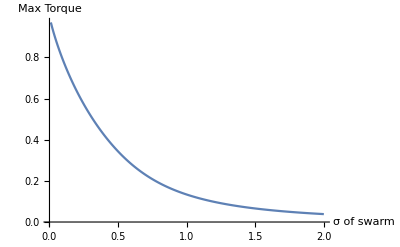

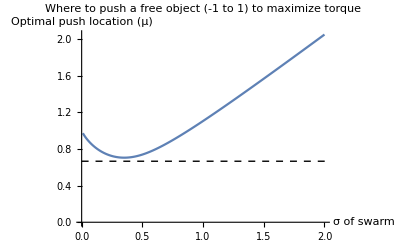

```mathematica
ListPlot[Transpose[{bestPushFree⟦;;,1⟧,bestPushFree⟦;;,2⟧}],AxesLabel->{"σ of swarm","Max Torque"},Joined->True]
ListPlot[{Transpose[{bestPushFree⟦;;,1⟧,bestPushFree⟦;;,3⟧}](*,
Transpose[{bestPush⟦;;,1⟧,2/3+1/3 ⅇ^(-6.5bestPush⟦;;,1⟧)}]*)},AxesLabel->{"σ of swarm","Optimal push location (μ)"},PlotRange->All,Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}]},PlotLabel->"Where to push a free object (-1 to 1) to maximize torque"]
```

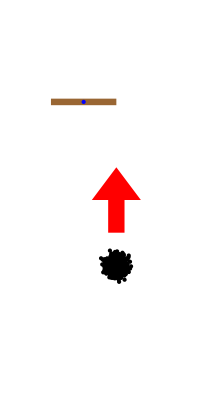
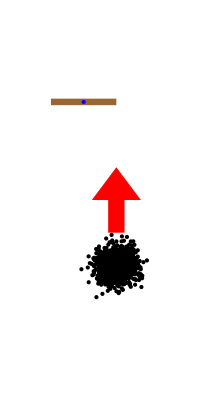
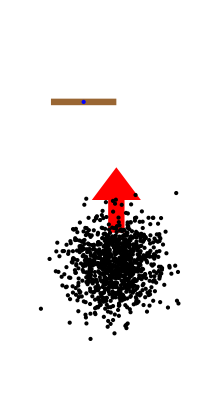
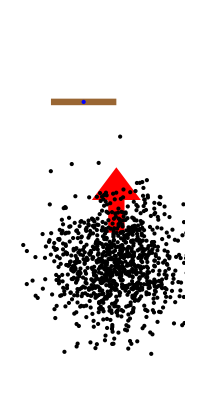
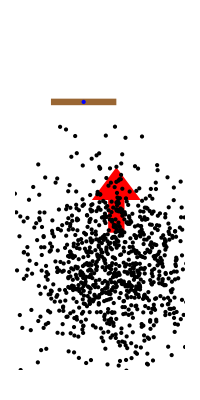

```mathematica
Table[Graphics[{
Brown,
Rectangle[{-1,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]
},
PlotRange->{{-2,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/50,1/10,1/2,1,2}}]
```

```mathematica
{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}
```

{{0.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{0.75,-3}}

### Problem 2: (Triangle dist) a free object (no pivot point). Where should swarm fit to generate the most torque?

```mathematica
FullSimplify[∫_-1^1 x pdfNormal[x,μ,σ]ⅆx](*assume the object COM is at 0, and the object extends from -1 to 1*)
```

((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)])

```mathematica
bestPushFree=Table[ans=FindMaximum[((-ⅇ^(-(-1+μ)^2/(2 σ^2))+ⅇ^(-(1+μ)^2/(2 σ^2))) σ)/(√(2 π))+1/2 μ (Erf[(1-μ)/(√2 σ)]+Erf[(1+μ)/(√2 σ)]),{μ,1}];{σ,First@ans,ans⟦2,1,2⟧},{σ,0.01,2,0.01}];
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum :: lstol will be suppressed during this calculation.

```mathematica
ListPlot[Transpose[{bestPushFree⟦;;,1⟧,bestPushFree⟦;;,2⟧}],AxesLabel->{"σ of swarm","Max Torque"},Joined->True]
ListPlot[{Transpose[{bestPushFree⟦;;,1⟧,bestPushFree⟦;;,3⟧}](*,
Transpose[{bestPush⟦;;,1⟧,2/3+1/3 ⅇ^(-6.5bestPush⟦;;,1⟧)}]*)},AxesLabel->{"σ of swarm","Optimal push location (μ)"},PlotRange->All,Joined->True,Epilog->{Dashed,Line[{{0,2/3},{100,2/3}}]},PlotLabel->"Where to push a free object (-1 to 1) to maximize torque"]
```

-Graphics-

-Graphics-

```mathematica
Table[Graphics[{
Brown,
Rectangle[{-1,-1/10},{1,1/10}],
Blue,Point[{0,0}],
Red,Polygon[{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}],
Black,PointSize[Tiny],Point[RandomVariate[MultinormalDistribution[{1,-5},{{σ,0},{0,σ}}],10^3]]
},
PlotRange->{{-2,3},{-8,2}},AxesOrigin->{0,0}],{σ,{1/50,1/10,1/2,1,2}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{{.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{.75,-3}}
```

{{0.75,-4},{1.25,-4},{1.25,-3},{1.75,-3},{1,-2},{1/4,-3},{0.75,-3}}

### Problem 3: given a variance σ if you push at location μ, with velocity v (everyone not in contact with the object moves at velocity v) , and variance bound σ_max, how long before you need to switch to variance control mode?